```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,i,items,nOrganisms},
path = StringForm["D:\\better output 2\\output\\frame``.json",frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
nOrganisms="o"/.items//CountDistinct;
nOrganisms
]
```

```mathematica
f0=0;
fMax=3269650;
df=1000;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames];
```

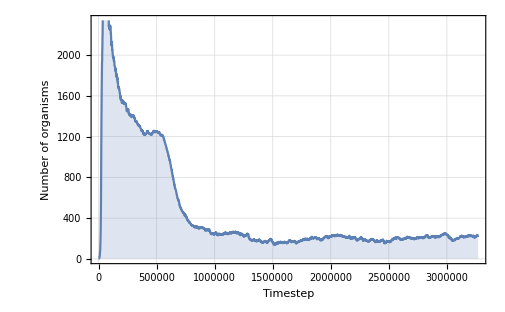

```mathematica
ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
GridLines->Automatic
]
```